This is a function to estimate the distance from a CY with a defining polynomial f, to the discriminant locus.
The method is to find the discrete solutions x_i of grad f=0 in each patch.
Then find the minimal normalized distance between one of these points and the manifold f=0, by 
constrained minimization of d(x,y)^2.
The first routine uses the Euclidean distance in the patch, 
and the second one uses the distance in P^n, which is cos^{-1} |z_1 \cdot \bar z_2|/|z_1|/|z_2|.
The second one is better motivated but somewhat slower.

Note that we have to run this once for each independent patch.  Often symmetry will relate the
results in different patches in which case we need not run it on all the patches.
For the function f, symmetry relates all patches.
For f2, symmetry relates (z1,z2,z5) and (z3,z4), so we need two runs.
Should the result depend on patch or not?? 
It should not - so this definition is not quite right.

A better definition, inspired by Shub et al 1999, is the following.  Let V be the space of coefficients of f.
Given a point Z_0 on the manifold, we define the linear subspace V_Z on which f(Z_0)=0.
There is then a linear subspace of this V_{Z,1} on which \partial f(Z_0)=0, which describes the
singular CYs where the singularity is at Z_0.  Given an f, we can compute the minimal geodesic distance
to V_{Z,1} (this only requires knowing the projection of f on  \partial f(Z_0)), and then minimize with respect to Z_0.  This also depends on a Euclidean metric on V, and we should choose one which is SU(5) invariant.
By discrete symmetry it is natural to take the standard metric on C^5, but given that we are assuming the geometry near Z_0 is almost singular, there might be a more natural choice.  But there is only a single adjustable coefficient so this is probably not interesting.
Working this out, one finds sin \theta = min_Z |\partial f(Z)|/||f|| |Z|^k where the derivatives and norm are taken over the homogeneous coordinates (no patches).

In these runs, NMinimize is searching complex values of the coordinates.
Complex parameters might work but they are too slow.

The conifold is psi=-5 in these conventions.

```mathematica
f = z1^5+z2^5+z3^5+z4^5+z5^5 + psi z1 z2 z3 z4 z5
```

z1^5+z2^5+z3^5+z4^5+psi z1 z2 z3 z4 z5+z5^5

```mathematica
f2 = f + phi (z3 z4^4+z3^2 z4^3+z3^3 z4^2+z3^4 z4)
```

z1^5+z2^5+z3^5+z4^5+phi (z3^4 z4+z3^3 z4^2+z3^2 z4^3+z3 z4^4)+psi z1 z2 z3 z4 z5+z5^5

```mathematica
Zsubs = {z1->x1 + I y1,z2->x2 + I y2,z3->x3 + I y3,z4->x4 + I y4,z5->x5 + I y5}
```

{z1→x1+ⅈ y1,z2→x2+ⅈ y2,z3→x3+ⅈ y3,z4→x4+ⅈ y4,z5→x5+ⅈ y5}

```mathematica
Weight[vec_] := (Times @@ Map[Factorial ,vec]) / Factorial[Length[vec]]
```

```mathematica
NormSquared[f_,vars_] := Plus @@ Map[ Weight[#[[1]]]Abs[#[[2]]]^2&,CoefficientRules[f,vars]]
```

```mathematica
NormSquared[f,{z1,z2,z3,z4,z5}]
```

5+Abs[psi]^2/120

```mathematica
XYsubs[vars_] := Variables[Apply[Times,vars] /. Zsubs]
```

```mathematica
EstimateModuliDistance[ f_, vars_, Zsubs_ ]  := Module[ {Zcsubs,grad,reim,len},
Zcsubs =  Zsubs /. I->-I;
len = Plus @@ ComplexExpand[(vars/.Zsubs)*(vars/.Zcsubs)];
grad = Grad[f,vars] ;
reim = ComplexExpand[ReIm[f] /. Zsubs];
m = NMinimize[{Plus @@ ComplexExpand[(grad/.Zsubs)*(grad/.Zcsubs)],0==  reim[[1]], 0==reim[[2]], 1==len }, XYsubs[vars]];
Sqrt[ Re[ m[[1]] / NormSquared[f,vars] ]]
]
```

Older definitions

```mathematica
EstimateDistanceInCPN[ f_, patch_, vars_] := Module[ {eqs,gradzero},
eqs = Map[#==0&,Grad[f /. patch -> 1 ,vars ]];
gradzero = DeleteDuplicates[Solve[eqs,vars]];
dmin[sol_] := Norm[Map[(# /. sol) - #&,vars]];
reim = ReIm[f/. patch -> 1];
MinimalBy[Map[NMinimize[{dmin[#],0==  reim[[1]], 0==reim[[2]]} /. Zsubs, 
XYsubs[vars]]&,gradzero],#[[1]]&]
]
```

```mathematica
EstimateTrueDistanceInCPN[ f_, patch_, vars_] := Module[ {eqs,gradzero},
eqs = Map[#==0&,Grad[f /. patch -> 1 ,vars ]];
gradzero = DeleteDuplicates[Solve[eqs,vars]];
dmin[sol_] := Abs[1+Total[Map[#  Conjugate[#/.sol]&,vars]]]^2/
(1+Norm[vars]^2)/(1+Norm[Map[(# /. sol)&,vars]]^2);
reim = ReIm[f/. patch -> 1];
res = MaximalBy[Map[NMaximize[{dmin[#],0==  reim[[1]], 0==reim[[2]] }/. Zsubs, 
XYsubs[vars]]&,gradzero],#[[1]]&];
Map[{ArcCos[#[[1]]]/Pi, #[[2]]}&, res]
]
```

```mathematica
d1[p_] := EstimateModuliDistance[f  /. psi->p, {z1,z2,z3,z4,z5}, Zsubs]
```

```mathematica
d1[-4.9]
```

0.0390084

```mathematica
T1 = Table[{psi,d1[psi]},{psi,-4.5,1,0.5}]
```

{{-4.5,0.0857035},{-4.,0.117858},{-3.5,0.142066},{-3.,0.158376},{-2.5,0.173988},{-2.,0.183199},{-1.5,0.189546},{-1.,0.195254},{-0.5,0.198811},{0.,0.2},{0.5,0.198854},{1.,0.204699}}

```mathematica
D1 = Interpolation[T1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {-4.89988} lies outside the range of data in the interpolating function. Extrapolation will be used.

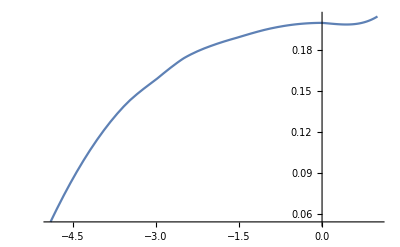

```mathematica
Plot[D1[p],{p,-4.9,1}]
```